```mathematica
Get[StringJoin[NotebookDirectory[],"PlaneCurvePlot.wl"]]
```

## Documentation

```mathematica
PlaneCurvePlot[{Cos[t],Sin[t]},{t,0,6}]
```

-Graphics-

```mathematica
?PlaneCurvePlot
```

## Examples

### Tangent

```mathematica
PlaneCurvePlot[{t,Sin[t]},{t,0,6},{1.5,4.1,5.1},TangentLineLength->20,PlotRange->{{-1,7},{-2,2}}]
```

-Graphics-

(* Serpentine *)

```mathematica
PlaneCurvePlot[{t,(3^2 t)/(2^2+t^2)},{t,-5,5},{-1,1.9},TangentLineLength->4]
```

-Graphics-

(* Deltoid *)

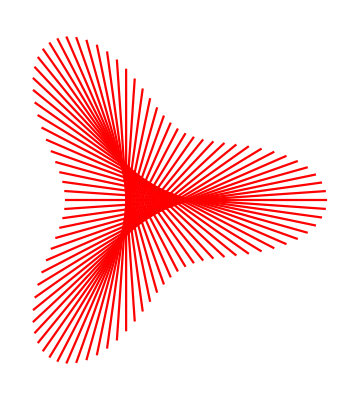

```mathematica
PlaneCurvePlot[{(2 Cos[t])/3+1/3 Cos[2 t],(2 Sin[t])/3-1/3 Sin[2 t]},{t,0,2 π,(2 π)/46},TangentLineLength->5,PlotCurve->False,PlotDot->False,Axes->False]
```

(* cycloid *)

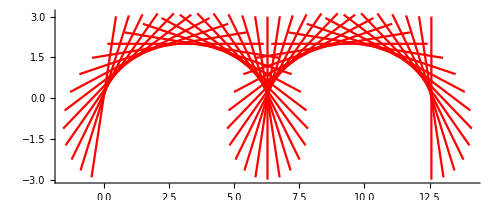

```mathematica
PlaneCurvePlot[{t-Sin[t],1-Cos[t]},{t,0,4 π,.31415},TangentLineLength->6,PlotCurve->False,PlotDot->False]
```

(* epitrochoid type curve *)

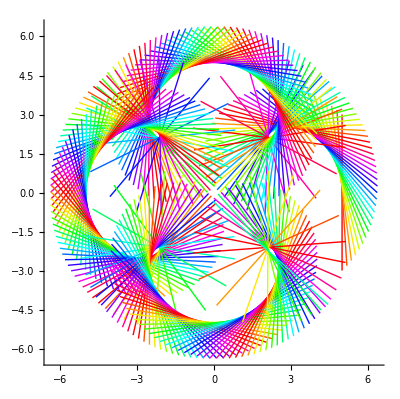

```mathematica
PlaneCurvePlot[{Cos[t]+Cos[t/5] 4,Sin[t]+Sin[t/5] 4},{t,0,9 π,.1},TangentLineLength->6,PlotDot->False,PlotCurve->False,TangentLineStyle->Table[{Hue[i]},{i,0,1,.05}]]
```

(* Tangent crawl *)

```mathematica
PlaneCurvePlot[{t,Cos[t]* Sin[t]+t},{t,-5,10},Range[3,5,0.05],TangentLineLength->6,PlotDot->False,PlotRange->{{-6,11},{-6,11}}]
```

-Graphics-

(* paint splash by tangent *)

```mathematica
PlaneCurvePlot[{t,2 Cos[t]+t},{t,-5,10,.1},TangentLineLength->60,PlotDot->False,PlotRange->{{-6,11},{-6,11}},TangentLineStyle->Table[Hue[i],{i,0,1,.02}]]
```

-Graphics-

## Normal

#### (* Parabola and its evolute Semi-cubic parabola *)

```mathematica
PlaneCurvePlot[{t,t^2},{t,-3,3,.1},NormalLineLength->15,NormalLineStyle->{Hue[0]},PlotDot->False,AspectRatio->Automatic,PlotRange->{{-6,6},{-2,5}}]
```

-Graphics-

#### (* two Astroids*)

```mathematica
PlaneCurvePlot[{(3 Cos[t])/4+1/4 Cos[3 t],(3 Sin[t])/4-1/4 Sin[3 t]},{t,0,2 π,(2 π)/80},NormalLineLength->3,CurveStyle->{Thickness[.007]},PlotRange->All,AspectRatio->Automatic,Axes->False]
```

-Graphics-

```mathematica
(* Cardioid *)
```

```mathematica
PlaneCurvePlot[{2 Cos[t]+Cos[2 t],2 Sin[t]+Sin[2 t]},{t,0,2 π,(2 π)/40},SecantConnection->{8,1},NormalLineLength->5,CurveStyle->{Thickness[.007]},AspectRatio->Automatic,PlotRange->{{-2.5,4},{-3.6,3.6}}]
```

-Graphics-

#### (* Archimedes' Spiral and its normal *)

```mathematica
PlaneCurvePlot[{t Cos[t],t Sin[t]},{t,0,4 π,.2},NormalLineLength->6,PlotDot->False,PlotRange->All,AspectRatio->Automatic]
```

-Graphics-

#### (* Ellipse and its Evolute *)

```mathematica
PlaneCurvePlot[{Cos[t],0.6 Sin[t]},{t,0,2 π,(2 π)/60},NormalLineLength->8,PlotDot->False,NormalLineStyle->{Hue[0,0,0]},CurveColorFunction->{Hue},CurveStyle->{Thickness[.007]},AspectRatio->Automatic,PlotRange->{{-2,2},{-2,2}}]
```

-Graphics-

#### (* deltoid normal beauty *)

```mathematica
PlaneCurvePlot[{(2 Cos[t])/3+1/3 Cos[2 t],(2 Sin[t])/3-1/3 Sin[2 t]},{t,0,2 π,(2 π)/120},NormalLineLength->1,PlotDot->False,SecantConnection->{60,1},Axes->False,AspectRatio->Automatic]
```

-Graphics-

#### (* Hypotrochoid normal beauty, {1,5/14,4/7} *)

```mathematica
PlaneCurvePlot[{(9 Cos[t])/14+4/7 Cos[(9 t)/5],(9 Sin[t])/14-4/7 Sin[(9 t)/5]},{t,0,5 2 π,(5 2 π)/140},NormalLineLength->1,Axes->False,AspectRatio->Automatic]
```

-Graphics-

#### (* hypotrochoid normal beauty, [1, 8/15, 8/15] *)

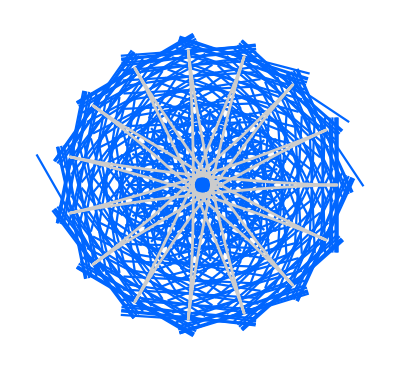

```mathematica
PlaneCurvePlot[{8/15 Cos[(7 t)/8]+(7 Cos[t])/15,-8/15 Sin[(7 t)/8]+(7 Sin[t])/15},{t,0,8 2 π,(8 2 π)/(15 20)},NormalLineLength->1,CurveColorFunction->{GrayLevel[.8]&},Axes->False,PlotDot->False,AspectRatio->Automatic]
```

#### (* "Cactus" *)

```mathematica
PlaneCurvePlot[t Cos[t]*{Cos[0.45* π* Cos[t]],Sin[0.45* π* Cos[t]]},{t,0,4.5 π,.05},NormalLineLength->.5,PlotCurve->True,PlotDot->False,AspectRatio->Automatic]
```

-Graphics-

## Secant

```mathematica
?SecantConnection
```

#### (* Circle*)

```mathematica
PlaneCurvePlot[{Cos[t/5],Sin[t/5]},{t,0,30,1},SecantConnection->{6,2},SecantLineStyle->{Hue[.4,.8,.7]},PlotParameterValue->True,DotStyle->{{PointSize[.02],Hue[.4,.8,.7]},{PointSize[.02],Hue[0]}},Ticks->None,PlotRange->All,AspectRatio->Automatic]
```

-Graphics-

#### (* Archimedes' Spiral with secants *)

```mathematica
PlaneCurvePlot[{t Cos[t],t Sin[t]},{t,0,10 π,(10 π)/120},PlotDot->False,SecantConnection->{10,1},SecantLineStyle->Table[Hue[i],{i,0,1,1/120}],PlotRange->{{-22.3,22},{-22,22.3}},Axes->False,AspectRatio->1]
```

-Graphics-

#### (* Equiangular spiral with secants; "Nautilus" *)

```mathematica
PlaneCurvePlot[{ⅇ^(t Cot[80 °]) Cos[t],ⅇ^(t Cot[80 °]) Sin[t]},{t,0,6 π,(6 π)/70},PlotDot->False,SecantConnection->{9,1},Axes->False,AspectRatio->Automatic,PlotRange->{{-18,28},{-22,13}}]
```

-Graphics-

#### (* Trisectrix of Maclaurin with secants *)

```mathematica
PlaneCurvePlot[{(-3+t^2)/(1+t^2),(t (-3+t^2))/(1+t^2)},{t,-3,3,.1},SecantConnection->{20,1},PlotRange->All,AspectRatio->Automatic]
```

-Graphics-

#### (* Folium of Descartes *)

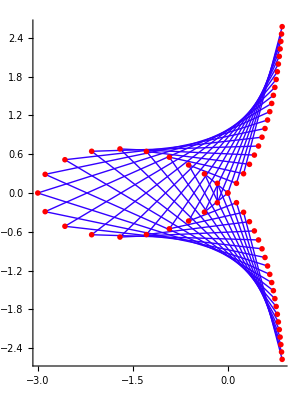

```mathematica
PlaneCurvePlot[{(3 (t^2-1))/(3 t^2+1),(3 t (t^2-1))/(3 t^2+1)},{t,-3,3,.1},PlotCurve->False,SecantConnection->{18,1},SecantLineStyle->{Hue[.7]},PlotRange->All,AspectRatio->Automatic]
```

#### (* Trochoid with colorful secants *)

```mathematica
PlaneCurvePlot[{t-2.2 Sin[t],1-2.2 Cos[t]},{t,0,3 2 π,.3},SecantConnection->{10,1},PlotDot->False,SecantLineStyle->Table[Hue[i],{i,0,1,1/62}],PlotRange->All,AspectRatio->Automatic]
```

-Graphics-

#### (* 8 Curve; Lemniscate of Gerono *)

```mathematica
PlaneCurvePlot[{Cos[t],Sin[t] Cos[t]},{t,0,6,.157},SecantConnection->{8,1},AspectRatio->Automatic]
```

-Graphics-

#### (* Hypotrochoid beauty, [1,3/5,2/3] *)

```mathematica
PlaneCurvePlot[{2/3 Cos[(2 t)/3]+(2 Cos[t])/5,-2/3 Sin[(2 t)/3]+(2 Sin[t])/5},{t,0,5 2 π,(3 2 π)/100},SecantConnection->{40,1},Axes->False,AspectRatio->Automatic]
```

-Graphics-

#### (* Hypotrochoid beauty, [1, 2/5, .13] *)

```mathematica
PlaneCurvePlot[{(3 Cos[t])/5+0.13 Cos[(3 t)/2],(3 Sin[t])/5-0.13 Sin[(3 t)/2]},{t,0,3 2 π,(2 2 π)/(5 22)},SecantConnection->{5 3,1},Axes->False,PlotDot->False,AspectRatio->Automatic]
```

-Graphics-

#### (* Hypotrochoid beauty, [1, 5/14, 4/7] *)

```mathematica
PlaneCurvePlot[{(9 Cos[t])/14+4/7 Cos[(9 t)/5],(9 Sin[t])/14-4/7 Sin[(9 t)/5]},{t,0,6 2 π,(5 2 π)/140},SecantConnection->{14,1},Axes->False,AspectRatio->Automatic]
```

-Graphics-

#### (* Hypotrochoid beauty, [1, 8/15, 8/15] *)

```mathematica
PlaneCurvePlot[{8/15 Cos[(7 t)/8]+(7 Cos[t])/15,-8/15 Sin[(7 t)/8]+(7 Sin[t])/15},{t,0,10 2 π,(8 2 π)/150},SecantConnection->{30,1},Axes->False,PlotDot->False,AspectRatio->Automatic]
```

-Graphics-

#### (* Flame *)

```mathematica
ParaPolarPlot[{Cos[t] t,1/2 π Cos[t]},{t,0,3 2 π,(3 2 π)/80},SecantConnection->{10,1},PlotCurve->True,PlotDot->False,PlotRange->{{-10,10},{-1,20}},PlotPoints->30,AspectRatio->Automatic]
```

ParaPolarPlot[{t Cos[t],1/2 π Cos[t]},{t,0,6 π,(3 π)/40},SecantConnection→{10,1},PlotCurve→True,PlotDot→False,PlotRange→{{-10,10},{-1,20}},PlotPoints→30,AspectRatio→Automatic]

#### (* croissant *)

```mathematica
ParaPolarPlot[{t,Cos[t] π},{t,0,3 2 π,(3 2 π)/300},SecantConnection->{10,1},AspectRatio->Automatic]
```

ParaPolarPlot[{t,π Cos[t]},{t,0,6 π,π/50},SecantConnection→{10,1},AspectRatio→Automatic]

## Caustic

```mathematica
PlaneCurvePlot[{1/4 (1-2 x+x^2)+1,x},{x,-2,4,.4},CausticLineLength->5,CausticOrigin->{2,1},PlotDot->False]
```

-Graphics-

Archimedes' Spiral

```mathematica
PlaneCurvePlot[{t Cos[t],t Sin[t]},{t,0,2 π,.2},CausticLineLength->20,PlotDot->False,PlotRange->{{-5,7},{-5,5}}]
```

-Graphics-

(* The catacaustic of the exponential curve with light rays parallel
to the y axes is the catenary. *)

```mathematica
PlaneCurvePlot[{t,E^t},{t,-5,2,.2},CausticOrigin->{0,2000},CausticLineLength->2100,PlotRange->{{-5,3},{-3,8}}]
```

-Graphics-

Caustic of an ellipse with light source from a focus.

```mathematica
PlaneCurvePlot[{2 Cos[t],1 Sin[t]},{t,0,2 π},Range[0.3,2.5,.18],CausticLineLength->3.9,CausticOrigin->{1.737,0},PlotDot->False,CausticLineStyle->{Hue[0],Hue[.8]},Epilog->{Hue[0],PointSize[.02],Point[{-1.737,0}]}]
```

-Graphics-

Caustic of Hyperbola with light source from a focus.

```mathematica
PlaneCurvePlot[{-Sec[t],Tan[t]},{t,-1.2,1.2},Range[0,1.2,.1],CausticLineLength->-10,CausticOrigin->{1.5,0},PlotDot->False,CurveColorFunction->{Hue[0]&},PlotRange->{{-3,2},{-2,2}}]
```

-Graphics-

(* diacaustic of a hyperbola at focus *)

```mathematica
PlaneCurvePlot[{-Sec[t],Tan[t]},{t,0,2 3.14,6.28/50},CausticLineLength->30,CausticOrigin->{√2,0},PlotDot->False,PlotRange->{{-4,4},{-4,4}},CausticLineStyle->Table[Hue[i],{i,0,1,1/50}]]
```

-Graphics-

(* Catacaustic of an ellipse *)

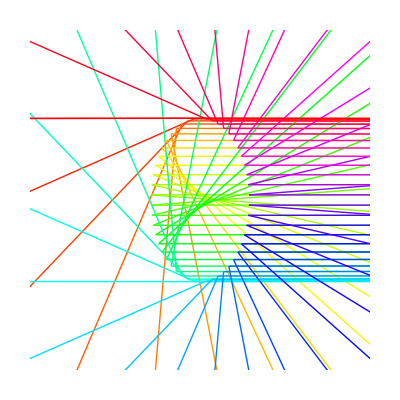

```mathematica
PlaneCurvePlot[{-1.2 Sin[t],2 Cos[t]},{t,0,2 π,(2 π)/50},CausticLineLength->2100,CausticOrigin->{2000,0},PlotDot->False,CurveColorFunction->{Hue[0]&},PlotCurve->False,CausticLineStyle->Table[Hue[i],{i,0,1,1/50}],PlotRange->{{-2,2} 2,2 {-2,2}},Axes->False]
```

(* diacaustic of an ellipse *)

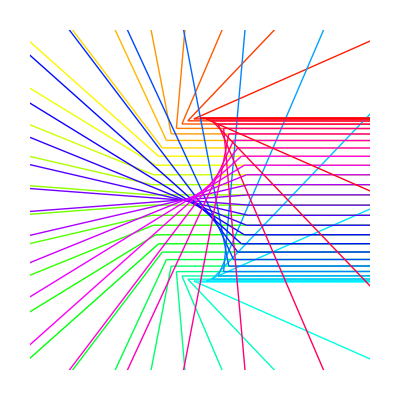

```mathematica
PlaneCurvePlot[{-1.2 Sin[t],2 Cos[t]},{t,0,2 π,(2 π)/50},CausticLineLength->-2100,CausticOrigin->{2000,0},PlotDot->False,CurveColorFunction->{Hue[0]&},PlotCurve->False,CausticLineStyle->Table[Hue[i],{i,0,1,1/50}],PlotRange->{{-2,2} 2,2 {-2,2}},Axes->False]
```

(* Cardioid by catacaustics of a circle.*)

```mathematica
PlaneCurvePlot[{Cos[t],Sin[t]},{t,0,2 π,(2 π)/60},CausticLineLength->5,CausticOrigin->{1,0},PlotDot->False,CurveColorFunction->{Hue[.7]&},PlotRange->{{-1.2,1.2},{-1.2,1.2}}]
```

-Graphics-

(* catacaustic of an Epitrochoid[1,3/5,.6]. *)

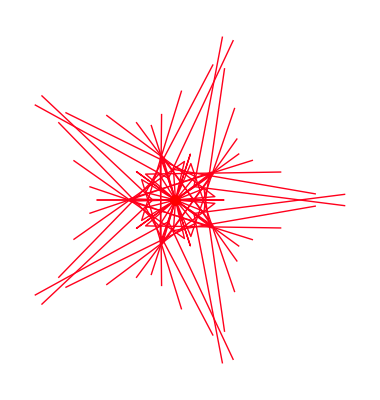

```mathematica
PlaneCurvePlot[{(8 Cos[t])/5+0.6 Cos[(8 t)/3],(8 Sin[t])/5+0.6 Sin[(8 t)/3]},{t,0,3 2 π,(3 2 π)/(5 9)},CausticLineLength->8,CausticOrigin->{0,0},PlotCurve->False,Axes->False,PlotDot->False,CurveColorFunction->{Hue[.45,1,.7]&},CausticLineStyle->{Hue[Random[]]}]
```

(* catacaustic of an Epitrochoid[1,1/4,.5]. *)

```mathematica
PlaneCurvePlot[{(5 Cos[t])/4+0.5 Cos[5 t],(5 Sin[t])/4+0.5 Sin[5 t]},{t,0,2 π,(2 π)/(4 30)},CausticLineLength->10,CausticOrigin->{0,0},CurveColorFunction->{Hue[.45,1,.7]&},CausticLineStyle->{Hue[Random[]]},Axes->False,PlotDot->False]
```

-Graphics-

(* catacaustic of an Epitrochoid[1, 1/6, 1]. *)

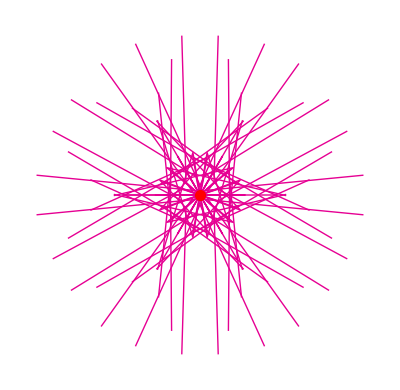

```mathematica
PlaneCurvePlot[{(7 Cos[t])/6+Cos[7 t],(7 Sin[t])/6+Sin[7 t]},{t,0,2 π,(2 π)/(6 11)},CausticLineLength->8,Axes->False,PlotDot->False,PlotCurve->False,CausticLineStyle->{{Hue[Random[],1,.9]}}]
```

## curvature, osculating circle, evolute

#### Osculating Circle

```mathematica
PlaneCurvePlot[{t,Sin[t]},{t,0,6},{1.5,5.1},PlotOsculatingCircle->True,PlotParameterValue->True,PlotEvolute->True]
```

-Graphics-

#### (* Equiangular Spiral with it's increasing curvature *)

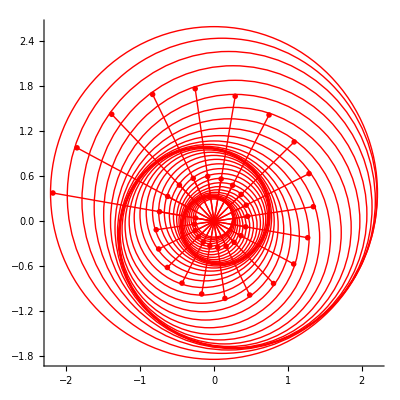

```mathematica
PlaneCurvePlot[{1/4 ⅇ^(t Cot[1.4]) Cos[t],1/4 ⅇ^(t Cot[1.4]) Sin[t]},{t,0,4 π,(4 π)/40},PlotOsculatingCircle->True,LineStyle->{Hue[0]},PlotRadial->True,PlotCurve->False,PlotDot->False]
```

#### (* Hypotrochoid osculating beauty, [1,3/8,.1] *)

```mathematica
PlaneCurvePlot[{(5 Cos[t])/8+0.1 Cos[(5 t)/3],(5 Sin[t])/8-0.1 Sin[(5 t)/3]},{t,0,3 2 π,(6 π)/32},PlotDot->False,PlotOsculatingCircle->True,CurveColorFunction->{Hue},CurveStyle->{Thickness[.015]},PlotRange->{{-2,2},{-2,2}},Background->Black]
```

-Graphics-

#### (* Hypotrochoid osculating beauty, [1,3/7,3/7] *)

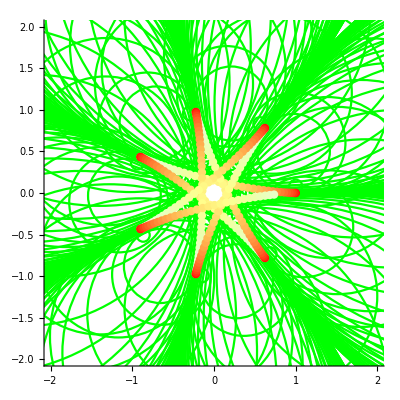

```mathematica
PlaneCurvePlot[{(4 Cos[t])/7+3/7 Cos[(4 t)/3],(4 Sin[t])/7-3/7 Sin[(4 t)/3]},{t,0.01,18.22,(3 2 π)/(7 41)},DotStyle->Table[{PointSize[.015],Hue[i,3.33 (.3-i),1]},{i,0,.3,(.3)/40}],PlotOsculatingCircle->True,PlotCurve->False,PlotRange->{{-2,2},{-2,2}}]
```

#### (* Hypotrochoid osculating beauty, [1,3/7,1] *)

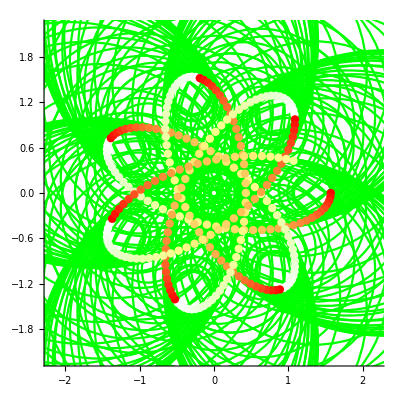

```mathematica
PlaneCurvePlot[{(4 Cos[t])/7+Cos[(4 t)/3],(4 Sin[t])/7-Sin[(4 t)/3]},{t,0,18.22,(3 2 π)/(7 40)},DotStyle->Table[{PointSize[.015],Hue[i,3.33 (.3-i),1]},{i,0,.3,(.3)/40}],PlotOsculatingCircle->True,PlotCurve->False,PlotRange->{{-2.2,2.2},{-2.2,2.2}}]
```

### Evolute

#### (* Illustration for understanding evolute and osculating circles *)

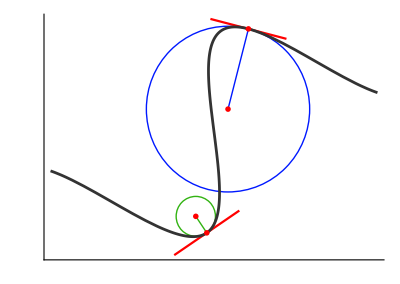

```mathematica
PlaneCurvePlot[{0.8+t Cos[34 °]-Sin[34 °] Sin[2 t],0.8+t Sin[34 °]+Cos[34 °] Sin[2 t]},{t,-2,2},{π/4+.3,-π/4},PlotEvolute->True,PlotOsculatingCircle->True,TangentLineLength->1,LineStyle->{{Hue[.65]},{Hue[.3,.9,.7]}},CurveColorFunction->{GrayLevel[.2]&},PlotRange->All,Ticks->None]
```

#### (* The evolute of a cycloid is another cycloid *)

```mathematica
PlaneCurvePlot[{t-Sin[t],1-Cos[t]},{t,0,2 2 π,(2 2 π)/60},PlotEvolute->True,LineStyle->{Hue[.43]}]
```

-Graphics-

#### (* The evolute of tracktrix is catenary *)

```mathematica
PlaneCurvePlot[{Log[Sec[t]+Tan[t]]-Sin[t],Cos[t]},{t,-1.53,1.53,.1},PlotEvolute->True,PlotRange->{{-3,3},{0,3}}]
```

-Graphics-

#### (* The evolute of astroid is another astroid *)

```mathematica
PlaneCurvePlot[{(3 Cos[t])/4+1/4 Cos[3 t],(3 Sin[t])/4-1/4 Sin[3 t]},{t,0,2 π,(2 π)/80},PlotEvolute->True,LineStyle->{Hue[0]},DotStyle->{Hue[.8]},Axes->False]
```

-Graphics-

#### (* 8 leaved rose and its evolute *)

```mathematica
PlaneCurvePlot[{Cos[4 t] Cos[t],Cos[4 t] Sin[t]},{t,0,2 π,(2 π)/120},PlotEvolute->True,LineStyle->{Hue[.43]}]
```

-Graphics-

## Radial

#### (* Parabola and its Radial *)

```mathematica
PlaneCurvePlot[{Cos[t],2 Sin[t]},{t,0,2 π,(2 π)/60},PlotRadial->True,PlotCurve->True,PlotDot->False,AspectRatio->Automatic]
```

-Graphics-

#### (* Radial of a cycloid is a circle *)

```mathematica
PlaneCurvePlot[{t-Sin[t],1-Cos[t]},{t,0,2 2 π,(2 2 π)/60},PlotRadial->True,LineStyle->{Hue[.43]},AspectRatio->Automatic]
```

-Graphics-

#### (* Radial of a catenary is Kampyle of Eudoxus *)

```mathematica
PlaneCurvePlot[{t,Cosh[t]},{t,-2,2,.15},PlotRadial->True,AspectRatio->Automatic,PlotRange->{{-10,10},{-1,4}}]
```

-Graphics-

#### (* Radial of astroid is a 4 leaved rose *)

```mathematica
PlaneCurvePlot[{(3 Cos[t])/4+1/4 Cos[3 t],(3 Sin[t])/4-1/4 Sin[3 t]},{t,0,2 π,(2 π)/100},PlotRadial->True,PlotDot->False,LineStyle->{Hue[0]},DotStyle->{{Hue[.9],PointSize[.01]}},AspectRatio->Automatic,Axes->False]
```

-Graphics-

#### (* Radial of Rose (a hypotrochoid) is another hypotrochoid *)

```mathematica
PlaneCurvePlot[{Cos[3 t] Cos[t],Cos[3 t] Sin[t]},{t,0,π,π/120},PlotRadial->True,PlotDot->False,LineStyle->{Hue[0]},AspectRatio->Automatic]
```

-Graphics-

## Conchoid

#### Conchoid of Nicomedes

```mathematica
PlaneCurvePlot[{x,1},{x,-3,3,.2},ConchoidSetting->{{0,0},{-2,2,1}},DotStyle->{Hue[0],Hue[.7],Hue[.8]},PlotDot->False]
```

-Graphics-

#### Limacon of Pascal

```mathematica
PlaneCurvePlot[{Sin[x],Cos[x]},{x,0,2 π,(2 π)/30},ConchoidSetting->{{0,-1},{-1,1}},PlotDot->False,PlotRange->{{-2,2},{-1.3,2.2}}]
```

-Graphics-

#### (* Conchoid of Sinusoid *)

```mathematica
PlaneCurvePlot[{x,Sin[x]},{x,0,10,0.25},ConchoidSetting->{{2,0},{-2,0,2}},PlotDot->False,DotStyle->{Hue[0],Hue[0.7],Hue[0.8]},PlotRange->{{-1,12},{-2,3}}]
```

-Graphics-

```mathematica
PlaneCurvePlot[{(3 Cos[t])/5+0.13 Cos[(3 t)/2],(3 Sin[t])/5-0.13 Sin[(3 t)/2]},{t,0,2 2 π,(2 2 π)/(5 20)},ConchoidSetting->{{0,0},{-.2,1}},Axes->False,PlotDot->False]
```

-Graphics-

#### (* Conchoid of an epitrochoid with parameter {1, 1/5, 2} *)

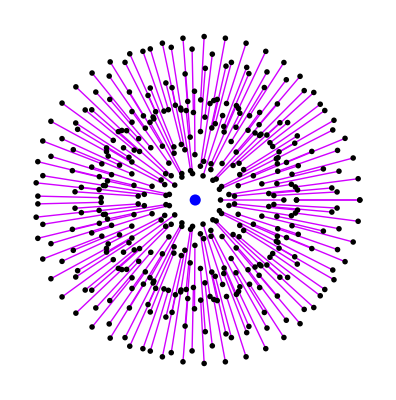

```mathematica
PlaneCurvePlot[{(6 Cos[t])/5+2 Cos[6 t],(6 Sin[t])/5+2 Sin[6 t]},{t,0,2 π,(2 π)/(5 40)},ConchoidSetting->{{0,0},{0,2}},Axes->False,PlotDot->False,PlotCurve->False,LineStyle->{{Hue[Random[]]}},DotStyle->{PointSize[.01]}]
```

## Inversion

#### (* Conics invert into Lemicon of Pascal at their focus *)

```mathematica
PlaneCurvePlot[{(0.7 Cos[t])/(1+0.7 Cos[t]),(0.7 Sin[t])/(1+0.7 Cos[t])},{t,0,2 π,(2 π)/40},InversionCircle->{{0,0},1},DotStyle->{{Hue[0],PointSize[.012]}}]
```

-Graphics-

#### (* Conics invert into Lemicon of Pascal at their focus *)

```mathematica
PlaneCurvePlot[{Cos[t]/(1+Cos[t]),Sin[t]/(1+Cos[t])},{t,-3,3,(2 π)/40},InversionCircle->{{0,0},1},DotStyle->{{Hue[0],PointSize[.012]}},PlotRange->{{-5,2.5},{-3.5,3.5}}]
```

-Graphics-

#### (* Conics invert into Lemicon of Pascal at their focus *)

```mathematica
PlaneCurvePlot[{(2 Cos[t])/(1+2 Cos[t]),(2 Sin[t])/(1+2 Cos[t])},{t,-3.14,3.14,(2 π)/40},InversionCircle->{{0,0},1},DotStyle->{{Hue[0],PointSize[.012]}},PlotRange->{{-1.5,3.5},{-3,3}}]
```

-Graphics-

#### Parabola invert into a Cissoid of Diocles Inversion point at the vertex of the parabola

```mathematica
PlaneCurvePlot[{t,t^2/4},{t,-20,20,.1},InversionCircle->{{0,0},5},DotStyle->{{Hue[0],PointSize[.01]}},PlotDot->False,PlotRange->{{-10,10},{-5.2,10}}]
```

-Graphics-

#### (* Rectangular hyperbola inverts into a Lemniscate of Bernoulli *) (* Inversion point at the hyperbola's center *)

```mathematica
PlaneCurvePlot[{-Sec[t],Tan[t]},{t,-π,π-.0001,(2 π)/(4 15)},InversionCircle->{{0,0},1},PlotDot->False,PlotRange->{{-3,3},{-3,3}}]
```

-Graphics-

#### (* Rectangular hyperbola inverts into strophoid *) (* Inversion point at the hyperbola's vertex *)

```mathematica
PlaneCurvePlot[{-Sec[t],Tan[t]},{t,-π,π-.0001,(2 π)/(4 15)},InversionCircle->{{1,0},1},PlotDot->False,PlotRange->{{-3,3},{-3,3}}]
```

-Graphics-

#### (* The inverse of an Archimedean spiral is another Archimedean spiral *)

```mathematica
PlaneCurvePlot[{t Cos[t],t Sin[t]},{t,0,4 π,(4 π)/50},InversionCircle->{{0,0},4},PlotDot->False]
```

-Graphics-

#### (* The inverse of a line with respect to a point not on the line is a circle. *)

```mathematica
PlaneCurvePlot[{t,1},{t,-5,5,.2},InversionCircle->{{0,0},2},PlotDot->False,PlotRange->{{-3,3},{-2.05,4.05}}]
```

-Graphics-

#### (* The inverse of a circle is a line. *)

```mathematica
PlaneCurvePlot[{Cos[t],Sin[t]},{t,-π,π,(2 π)/40},InversionCircle->{{0,-1},1.5},PlotDot->False,PlotRange->{{-4,4},{-2.5,1.2}}]
```

-Graphics-

```mathematica
(* Inverse of a rose is an epispiral *)
```

```mathematica
PlaneCurvePlot[{Cos[t] Cos[4 t],Cos[4 t] Sin[t]},{t,0,2 π,(2 π)/320},InversionCircle->{{0,0},1},PlotDot->False,DotStyle->{{PointSize[.007],Hue[0]}},PlotRange->{{-4,4},{-4,4}}]
```

-Graphics-

## Involute

#### (* Involute of a circle *)

```mathematica
PlaneCurvePlot[{Cos[t],Sin[t]},{t,0,2 π,(2 π)/40},PlotInvolute->True]
```

-Graphics-

#### (* The involute of catenary is tractrix *)

```mathematica
PlaneCurvePlot[{t,Cosh[t]},{t,-2,2.5},Range[0,5,.25],PlotInvolute->True,PlotRange->{{-2.05,5},{-0.05,6.05}}]
```

-Graphics-

#### (* the involute of sinusoid *)

```mathematica
PlaneCurvePlot[{t,Sin[t]},{t,0,2 π,(2 π)/80},PlotInvolute->True,PlotDot->False]
```

-Graphics-

## Parallel

#### (* Sinusoid and its parallel *)

```mathematica
PlaneCurvePlot[{t,Sin[t]},{t,0,3 π,.1},ParallelCurveOffset->{3},NormalLineLength->6,PlotDot->False,NormalLineStyle->{Hue[.17]},AspectRatio->Automatic,PlotRange->{{-2.5,11.5},{-2,4}}]
```

-Graphics-

#### (* Lemniscate of Bernoulli and its parallel *)

```mathematica
PlaneCurvePlot[{Cos[t]/(1+Sin[t]^2),(Sin[t] Cos[t])/(1+Sin[t]^2)},{t,0,2 π,.07},ParallelCurveOffset->{.175,.35,.7},PlotDot->False,DotStyle->{Hue[.9],Hue[.7],Hue[0]},AspectRatio->Automatic,PlotRange->All]
```

-Graphics-

#### (*3 leaved rose and its parallel *)

```mathematica
PlaneCurvePlot[{Cos[3 t] Cos[t],Cos[3 t] Sin[t]},{t,0,π,.015},ParallelCurveOffset->{.18,.4,.6},PlotDot->False,DotStyle->{Hue[0],Hue[.3],Hue[.7]},AspectRatio->Automatic,PlotRange->All]
```

-Graphics-

#### (* Astroid and its parallel *)

```mathematica
PlaneCurvePlot[{(3 Cos[t])/4+1/4 Cos[3 t],(3 Sin[t])/4-1/4 Sin[3 t]},{t,0,2 π,(2 π)/160},ParallelCurveOffset->{.3,.5,1},PlotDot->False,CurveStyle->{Thickness[.007]},DotStyle->{Hue[.6],Hue[.8],Hue[0]},AspectRatio->Automatic,Axes->False]
```

-Graphics-

#### (* Hypotrochoid parallel beauty, [1,1/5,.13] *)

```mathematica
PlaneCurvePlot[{(4 Cos[t])/5+0.13 Cos[4 t],(4 Sin[t])/5-0.13 Sin[4 t]},{t,0,2 π,(2 π)/(5 30)},ParallelCurveOffset->Table[i,{i,-.5,.5,.1}],Axes->False,PlotDot->False,DotStyle->Table[Hue[Random[]],{20}],AspectRatio->Automatic]
```

-Graphics-

#### (* Hypotrochoid parallel beauty. Rotate[Hypocycloid[3][t], Pi/2] *)

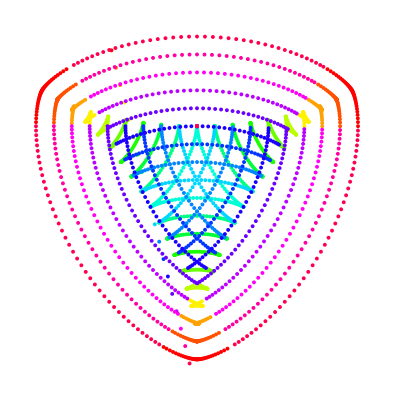

```mathematica
Clear[myOffset,myStyle];
myOffset=Table[i,{i,-3,3,6/18}];
myStyle=Table[{Hue[i],PointSize[.007]},{i,0,1,1/Length[myOffset]}];
PlaneCurvePlot[{-(2 Sin[t])/3+1/3 Sin[2 t],(2 Cos[t])/3+1/3 Cos[2 t]},{t,0,2 π,(2 π)/(3 40)},ParallelCurveOffset->myOffset,PlotDot->False,PlotCurve->False,DotStyle->myStyle,LineStyle->{GrayLevel[0]},Axes->False,AspectRatio->Automatic]
Clear[myOffset,myStyle];
```

## Pedal

#### (* Pedal of a circle is the Limacon of Pascal *)

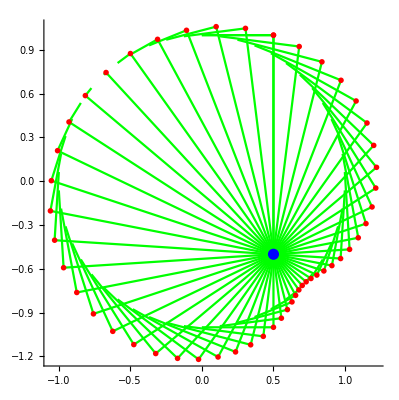

```mathematica
PlaneCurvePlot[{Sin[t],Cos[t]},{t,0,2 π,(2 π)/50},PedalPoint->{.5,-.5},PlotCurve->False,PlotDot->False,AspectRatio->Automatic]
```

#### (* Pedal of astroid with respect to its center is 4 leaved rose *)

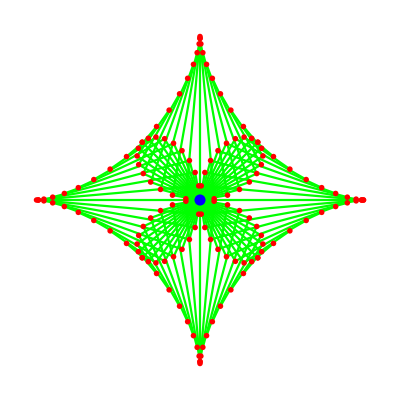

```mathematica
PlaneCurvePlot[{(3 Cos[t])/4+1/4 Cos[3 t],(3 Sin[t])/4-1/4 Sin[3 t]},{t,0,2 π,(2 π)/(4 18)},PlotCurve->False,PedalPoint->{0,0},Axes->False,AspectRatio->Automatic]
```

#### (* Pedal of a hyperbola with respect to its focus is a circle *)

```mathematica
PlaneCurvePlot[{-Sec[t],Tan[t]},{t,-1.2,1.2},Range[-1.5,1.5,.1],PedalPoint->{1.5,0},PlotDot->False,CurveColorFunction->{Hue[0]&},AspectRatio->Automatic,PlotRange->{{-2.4,1.8},{-2,2}}]
```

-Graphics-

#### (* Pedal of a hyperbola with respect to its center is lemniscate of Bernoulli *)

```mathematica
PlaneCurvePlot[{-Sec[t],Tan[t]},{t,-1.2,1.2},Range[-1.5,1.5,.1],PedalPoint->{0,0},PlotDot->False,CurveColorFunction->{Hue[0]&},AspectRatio->Automatic,PlotRange->{{-2,.05},{-1.5,1.5}}]
```

-Graphics-

#### (* Pedal of Parabola with respect to its focus is a line *)

```mathematica
PlaneCurvePlot[{t,t^2/2},{t,-2,2,.2},PedalPoint->{0,1/2},PlotDot->False,DotStyle->{{Hue[0],PointSize[.02]}},LineStyle->{Hue[0]},CurveStyle->{Thickness[.008]},AspectRatio->Automatic,PlotRange->{{-1.2,1.2},{-.2,.8}},Axes->True]
```

-Graphics-

#### (* Pedal of an ellipse with respect to its focus is a circle *)

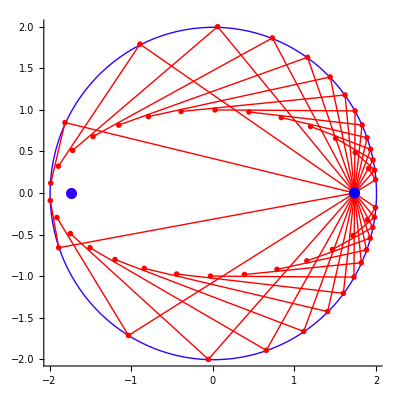

```mathematica
PlaneCurvePlot[{2 Cos[t],1 Sin[t]},{t,0,2 π},Range[0.3,6,(2 π)/30],PedalPoint->{1.737,0},PlotDot->True,LineStyle->{Hue[0]},PlotCurve->False,PlotRange->All,AspectRatio->Automatic,Prolog->{Hue[0.7],PointSize[.02],Point[{-1.737,0}],Hue[0.7],Circle[{0,0},2]}]
```

#### (* Hypotrochoid beauty. [1,2/3,.4] *)

```mathematica
PlaneCurvePlot[{0.4 Cos[t/2]+Cos[t]/3,-0.4 Sin[t/2]+Sin[t]/3},{t,0,2 2 π,(2 2 π)/(5 18)},PedalPoint->{0,0},Axes->False,PlotDot->False,AspectRatio->Automatic]
```

-Graphics-

#### (* Hypotrochoid beauty, [1, 3/4, .5] *)

```mathematica
PlaneCurvePlot[{0.5 Cos[t/3]+Cos[t]/4,-0.5 Sin[t/3]+Sin[t]/4},{t,0,3 2 π,(3 2 π)/(4 20)},PedalPoint->{0,0},Axes->False,PlotDot->False,LineStyle->{Hue[Random[]]},AspectRatio->Automatic]
```

-Graphics-